```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]]
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3+ⅈ (y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3)

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

```mathematica
imaginary = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
```

```mathematica
mat = {{D[real,x],D[real,y]},{D[imaginary,x],D[imaginary,y]}};
mat2 ={{D[D[real,x],x],D[D[real,y],y]},{D[D[imaginary,x],x],D[D[imaginary,y],y]}};
```

```mathematica
autovj = Eigenvalues[mat];
autovh = Eigenvalues[mat2];
eigenvecj = Eigensystem[mat];
eigenvech = Eigensystem[mat2];
```

```mathematica
n=8;
L={};
For[i=38 300,i<384 30,i++;
μ=i/3000.;
For[j=1,j<10,j++;
x0=RandomReal[];
y0=RandomReal[] 10^-1;
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,y0}}];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,-y0}}];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
]
]
L = DeleteDuplicates[L];
Clear[μ]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPointPlot3D[L,ViewPoint->{0,0,Infinity}];
ListPointPlot3D[L]
```

-Graphics3D-

```mathematica
tab1=FindRoot[{Re[map3[x,y,3.80]]== x,Im[map3[x,y,3.80]]== y},{{x,0.7},{y,0.1}}];
tab1⟦2,2⟧;
Round[tab1⟦2,2⟧10^8] 10^-8;
```

```mathematica
Lnum = {}
For[i=0,i<Length[L],i++;
AppendTo[Lnum,L⟦i⟧];
AppendTo[Lnum⟦i⟧,i]]
```

{}

```mathematica
afterw = Select[L,#⟦1⟧>3.8284 &];
beforew=Select[L, #⟦1⟧<3.8284 &];
```

```mathematica
ListPointPlot3D[beforew];
```

```mathematica
pontos = L;
groupA = Select[pontos, #⟦2⟧<0.1 &];
groupBstep = Select[pontos, #⟦2⟧>0.1 &];
groupB = Select[groupBstep, #⟦2⟧<0.2 &];
groupCstep = Select[pontos, #⟦2⟧>0.4 &];
groupC= Select[groupCstep, #⟦2⟧<0.6 &];
groupDstep = Select[pontos, #⟦2⟧>0.6 &];
groupD = Select[groupDstep, #⟦2⟧<0.8 &];
groupE = Select[pontos, #⟦2⟧>0.8 &];

ListPointPlot3D[groupB]
```

-Graphics3D-

```mathematica
groups = { groupB, groupC, groupE};
thelistp = {{},{},{}};
thelistf = {{},{},{}};
```

thelistf -->  lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverão 8 termos:  {gp1xf, gp1yf, gp2xf, gp2yf, ... }, sendo cada termo uma função interpolada de μ com relação a x ou y de cada ramo de um grupo (B1, B2, B3, B4).

thelistp -> lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverão 4 termos:  {gp1, gp2, gp3, gp4 }, sendo cada termo uma lista contendo {μ, x, y} referentes a cada ramo de um grupo  (B1, B2, B3, B4).

```mathematica
For[i=0,i<Length[groups],i++;
before = Select[groups⟦i⟧,#⟦1⟧<3.8284 &];
after = Select[groups⟦i⟧, #⟦1⟧>3.8284 &];
gp1 = Select[before, #⟦3⟧>0 &];
gp3 = Select[before, #⟦3⟧<0 &];
gp2 = Select[after,#⟦2⟧>before⟦Length[before],2⟧ &];
gp4 = Select[after,#⟦2⟧<before⟦Length[before],2⟧ &];
(* step com drop adicionado*)
gp1x = DeleteDuplicates[Drop[gp1,0,{3}]];
gp1y = DeleteDuplicates[Drop[gp1,0,{2}]];
gp2x = DeleteDuplicates[Drop[gp2,0,{3}]];
gp2y = DeleteDuplicates[Drop[gp2,0,{2}]];
gp3x = DeleteDuplicates[Drop[gp3,0,{3}]];
gp3y =DeleteDuplicates[Drop[gp3,0,{2}]];
gp4x = DeleteDuplicates[Drop[gp4,0,{3}]];
gp4y =DeleteDuplicates[Drop[gp4,0,{2}]];
gp1xf = Interpolation[gp1x];
gp1yf = Interpolation[gp1y];
gp2xf = Interpolation[gp2x];
gp2yf = Interpolation[gp2y];
gp3xf = Interpolation[gp3x];
gp3yf = Interpolation[gp3y];
gp4xf = Interpolation[gp4x];
gp4yf = Interpolation[gp4y];
AppendTo[thelistp⟦i⟧,gp1] ;
AppendTo[thelistp⟦i⟧,gp2];
AppendTo[thelistp⟦i⟧,gp3];
AppendTo[thelistp⟦i⟧,gp4];
AppendTo[thelistf⟦i⟧,gp1xf];
AppendTo[thelistf⟦i⟧,gp1yf];
AppendTo[thelistf⟦i⟧,gp2xf];
AppendTo[thelistf⟦i⟧,gp2yf];
AppendTo[thelistf⟦i⟧,gp3xf];
AppendTo[thelistf⟦i⟧,gp3yf];
AppendTo[thelistf⟦i⟧,gp4xf];
AppendTo[thelistf⟦i⟧,gp4yf];]
```

Interpolation::inddp: The point 3.81533 in dimension 1 is duplicated.

autovjlist -->  lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverão 4 termos:  {autovj1, autovj2, ...}, sendo cada termo uma função interpolada de μ com relação a seu autovalor de cada ramo de um grupo (B1, B2, B3, B4) da matriz jacobiana.

autovhlist -->  lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverão 4 termos:  {autovh1, autovh2, ...}, sendo cada termo uma função interpolada de μ com relação a seu autovalor de cada ramo de um grupo (B1, B2, B3, B4) da matriz hessiana.

```mathematica
autovjlist = {}
autovhlist = {}
For[i=0,i<Length[groups],i++;
autovj1 [μ_]:= autovj/.{x-> thelistf⟦i,1⟧[μ],y-> thelistf⟦i,2⟧[μ]};
autovj2 [μ_]:= autovj/.{x-> thelistf⟦i,3⟧[μ],y-> thelistf⟦i,4⟧[μ]};
autovj3 [μ_]:= autovj/.{x-> thelistf⟦i,5⟧[μ],y-> thelistf⟦i,6⟧[μ]};
autovj4 [μ_]:= autovj/.{x-> thelistf⟦i,7⟧[μ],y-> thelistf⟦i,8⟧[μ]};
autovjgroup = {autovj1[μ], autovj2[μ], autovj3[μ], autovj4[μ]};
AppendTo[autovjlist, autovjgroup];
autovh1 [μ_]:= autovh/.{x-> thelistf⟦i,1⟧[μ],y-> thelistf⟦i,2⟧[μ]};
autovh2 [μ_]:= autovh/.{x-> thelistf⟦i,3⟧[μ],y-> thelistf⟦i,4⟧[μ]};
autovh3 [μ_]:= autovh/.{x-> thelistf⟦i,5⟧[μ],y-> thelistf⟦i,6⟧[μ]};
autovh4 [μ_]:= autovh/.{x-> thelistf⟦i,7⟧[μ],y-> thelistf⟦i,8⟧[μ]};
autovhgroup = {autovh1[μ], autovh2[μ], autovh3[μ], autovh4[μ]};
AppendTo[autovhlist, autovhgroup]]
```

{}

{}

```mathematica
autovjlist⟦1,1⟧/. μ -> 3.825
```

{-1.40828,1.40828}

```mathematica
autovhlist⟦1,1,2⟧/. μ -> 3.81
```

-200.472

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

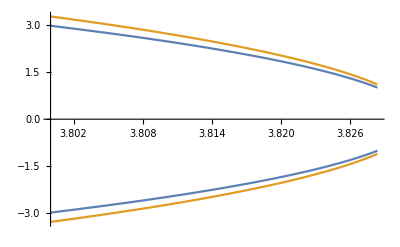

```mathematica
Plot[{autovjlist⟦1,1⟧,1.1autovjlist⟦1,3⟧},{μ,3.8,3.8284}]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

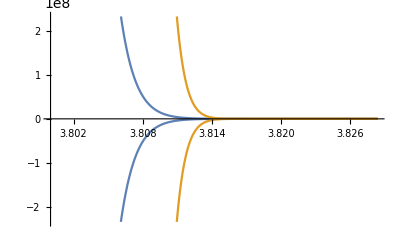

```mathematica
Plot[{autovjlist⟦1,2⟧,1.1autovjlist⟦1,4⟧},{μ,3.8,3.8284}]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

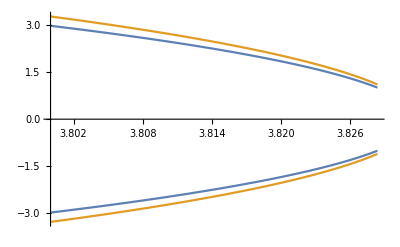

```mathematica
Plot[{autovjlist⟦2,1⟧,1.1autovjlist⟦2,3⟧},{μ,3.8,3.8284}]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

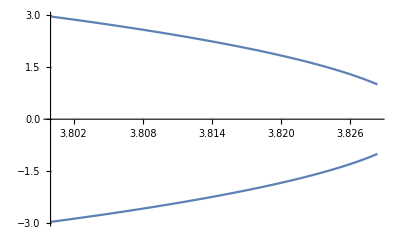

```mathematica
Plot[{autovjlist⟦3,1⟧,1.1autovjlist⟦3,3⟧},{μ,3.8,3.8284}]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

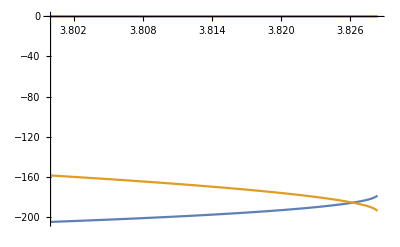

```mathematica
Plot[{autovhlist⟦1,1⟧,1.1autovhlist⟦1,3⟧},{μ,3.8,3.8284}]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

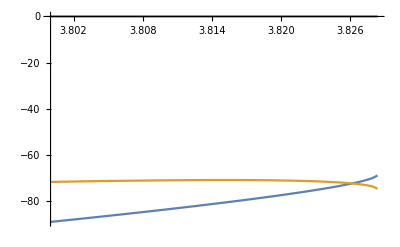

```mathematica
Plot[{autovhlist⟦2,1⟧,1.1autovhlist⟦2,3⟧},{μ,3.8,3.8284}]
```

Abaixo, comportamento que indica que o grupo E possui pouca contribuição (...), porque o inverso da frequência (...) ----> buscar entender melhor <-----

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

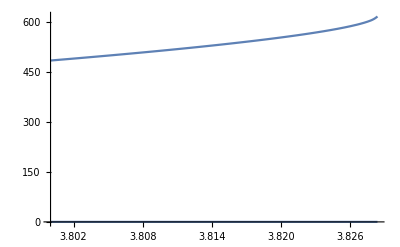

```mathematica
Plot[{autovhlist⟦3,1⟧,1.1autovhlist⟦3,3⟧},{μ,3.8,3.8284}]
```

Código com a mesma funcionalidade de autovjlist para testar o funcionamento de forma separada de cada elemento que estaria contido na lista.
Em seguida, um plot dos autovalores em função de μ para os 4 autovj’s.

```mathematica
autovj1 [μ_]= autovj/.{x-> thelistf⟦1,1⟧[μ],y-> thelistf⟦1,2⟧[μ]};
autovj2 [μ_]= autovj/.{x-> thelistf⟦1,3⟧[μ],y-> thelistf⟦1,4⟧[μ]};
autovj4 [μ_]= autovj/.{x-> thelistf⟦1,7⟧[μ],y-> thelistf⟦1,8⟧[μ]};
autovj3 [μ_]= autovj/.{x-> thelistf⟦1,5⟧[μ],y-> thelistf⟦1,6⟧[μ]};
```

```mathematica
autovj1[3.825]
```

{-1.40828,1.40828}

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

Interpolation::inddp: The point 3.833 in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.82864} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

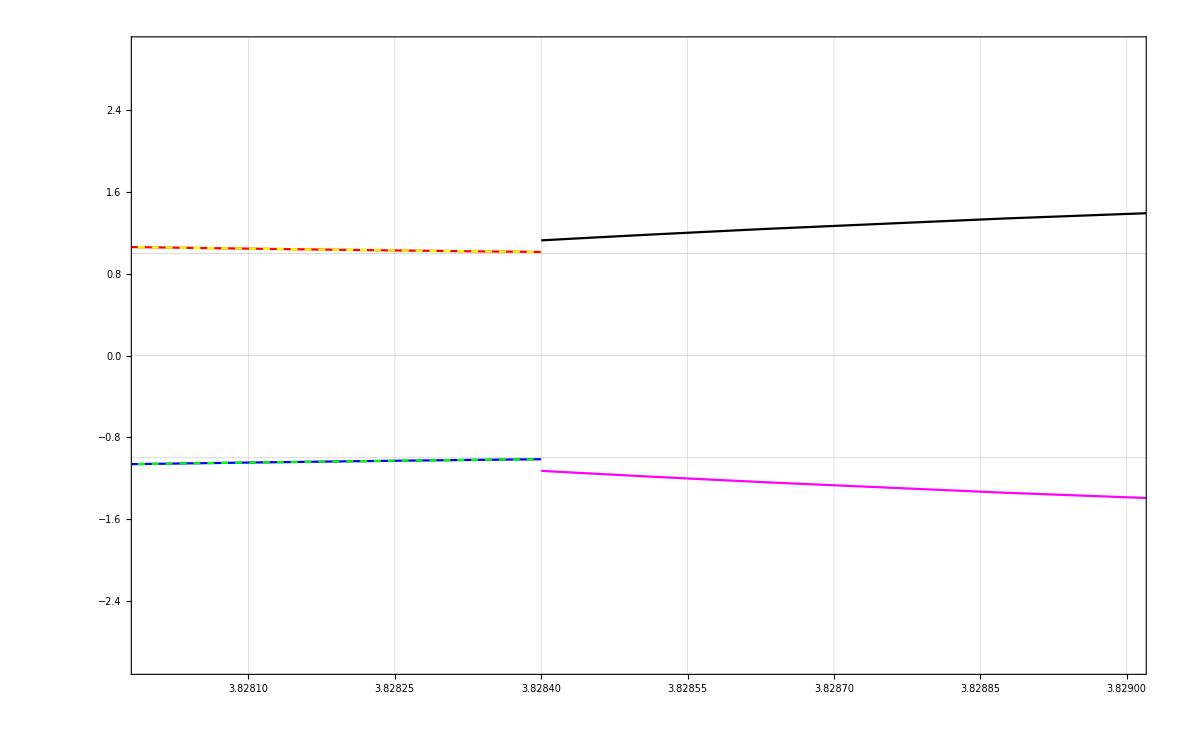

```mathematica
Show[
Plot[autovj1[μ]⟦1⟧,{μ,3.82,3.8284},PlotRange->{{3.828,3.829},{-3,3}},PlotStyle->Blue,Frame->True,GridLines->{Automatic, {-1,0,1}}],Plot[autovj1[μ]⟦2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->Red],
Plot[autovj2[μ]⟦1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Brown],
Plot[autovj2[μ]⟦2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Orange],
Plot[autovj3[μ]⟦1⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Green,Dashed}],
Plot[autovj3[μ]⟦2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Yellow,Dashed}],
Plot[autovj4[μ]⟦1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Magenta],
Plot[autovj4[μ]⟦2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Black]
]
```

Tentativas de calcular uma média ponderada dos autovalores da Hessiana.

```mathematica
xyz[μ_]= (thelistf⟦1,1⟧[μ])/autovhlist⟦1,1,2⟧+(thelistf⟦1,3⟧[μ])/autovhlist⟦1,3,2⟧+(thelistf⟦2,1⟧[μ])/autovhlist⟦2,1,2⟧+(thelistf⟦2,3⟧[μ])/autovhlist⟦2,3,2⟧+(thelistf⟦3,1⟧[μ])/autovhlist⟦3,1,2⟧+(thelistf⟦3,3⟧[μ])/autovhlist⟦3,3,2⟧;
```

```mathematica
xx[μ_]= (thelistf⟦2,1⟧[μ])/autovhlist⟦2,1,2⟧;
```

```mathematica
xyz[3.82];
```

InterpolatingFunction::dmval: Input value {3.82} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
autovhlist⟦3,3,2⟧/. μ-> 3.828;
```

```mathematica
thelistf⟦3,3⟧
```

InterpolatingFunction[…]

```mathematica
xx[3.82]
```

-0.00664957

```mathematica
thelistf⟦1,1⟧
```

InterpolatingFunction[…]

```mathematica
qwa[μ_] = autovhlist⟦1,1,2⟧;
```

```mathematica
qwa[3.82]
```

-193.588